```mathematica
(* Plotting package *)
<<MaTeX`
rasterListContourPlot[pList_,opts:OptionsPattern[]]:=Module[{img,cont,contL,plotRangeRule,contourOptions,frameOptions,rangeCoords},contourOptions=Join[FilterRules[{opts},FilterRules[Options[ListContourPlot],Except[{Background,Frame,Axes}]]],{Frame->None,Axes->None}];
contL=ListContourPlot[pList,Evaluate@Apply[Sequence,contourOptions]];
cont=First[Cases[{contL},Graphics[__],Infinity]];
img=Rasterize[Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,1]]],PlotRangePadding->None,ImagePadding->None,Options[cont,PlotRange]],"Image",ImageSize->With[{size=Total[{2,0} (ImageSize/.{opts})/.{ImageSize->CurrentValue[ImageSize]}]},If[NumericQ[size],size,First[WindowSize/.Options[EvaluationNotebook[]]]]]];
plotRangeRule=FilterRules[AbsoluteOptions[cont],PlotRange];
rangeCoords=Transpose[PlotRange/.plotRangeRule];
frameOptions=Join[FilterRules[{opts},FilterRules[Options[Graphics],Except[{PlotRangeClipping,PlotRange}]]],{plotRangeRule,Frame->True,PlotRangeClipping->True}];
If[Head[contL]===Legended,Legended[#,contL[[2]]],#]&@Show[Graphics[{Inset[Show[SetAlphaChannel[img,"ShadingOpacity"/.{opts}/.{"ShadingOpacity"->1}],AspectRatio->Full],rangeCoords[[1]],{0,0},rangeCoords[[2]]-rangeCoords[[1]]]},PlotRangePadding->None],Graphics[GraphicsComplex[cont[[1,1]],cont[[1,2,2]]]],Evaluate@Apply[Sequence,frameOptions]]]
(* These functions can basically be ignored. It's just dealing with the graphics for when I want to format my publication-quality plots. *)
Clear[undistortedGraphicsColumn];
Options[undistortedGraphicsColumn]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsColumn[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,width, xsizes, ysizes},width=Max@sizes[[All,1]];
ysizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@list-1]];
xsizes = sizes[[All, 1]];
Graphics[Table[Inset[list[[i]],{(width - xsizes[[i]]) / 2,-Plus@@ysizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{width,Plus@@ysizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@ysizes,0}},AspectRatio->Plus@@ysizes/width,PlotRangePadding->None]]

Clear[undistortedGraphicsRow];
Options[undistortedGraphicsRow]=Join[{Spacings->0},Options[Graphics]];
undistortedGraphicsRow[list_, opts:OptionsPattern[]]:=Module[{sizes=ImageDimensions/@list,height, xsizes, ysizes},height=Max@sizes[[All,2]];
xsizes=sizes[[All,1]]+Join[ConstantArray[OptionValue[Spacings],Length@list-1],{0}];
ysizes = sizes[[All, 2]];
Graphics[Table[Inset[list[[i]],{If[i>1, Plus@@xsizes[[;;i-1]],0], (height-ysizes[[i]])/2},ImageScaled[{0,0}]],{i,Length[list]}],ImageSize->{Plus@@xsizes, height},ImagePadding->None,PlotRange->{{0, Plus@@xsizes}, {0, height}},AspectRatio->height/(Plus@@xsizes),PlotRangePadding->None]]

Clear[format]
Options[format] = Options[PaddedForm];
format[x_, sd_]:=Module[{m,e},
{m,e} = MantissaExponent[x];
If[x == 0, "0",If[-2≤e≤2,ToString[PaddedForm[x, sd]],ToString[PaddedForm[ToExpression[ToString[m]]*10, sd]]<>"\\times10^{"<>ToString[e-1]<>"}"]]
]
```

```mathematica
AllNeighbors = Compile[{{i, _Integer}, {sqrtlenfpoints, _Integer}},
(* First handle the four corners *)
If[i==1, {2, sqrtlenfpoints+1},
If[i==sqrtlenfpoints, {sqrtlenfpoints - 1, 2 sqrtlenfpoints},
If[i==sqrtlenfpoints^2-sqrtlenfpoints+1, {sqrtlenfpoints^2-2sqrtlenfpoints+1, sqrtlenfpoints^2-sqrtlenfpoints+2},
If[i==sqrtlenfpoints^2, {sqrtlenfpoints^2-1, sqrtlenfpoints^2-sqrtlenfpoints},
(* Then handle the top and bottom boundary *)
If[1<i<sqrtlenfpoints, {i-1, i+1, i+sqrtlenfpoints},
If[sqrtlenfpoints^2-sqrtlenfpoints+1<i<sqrtlenfpoints^2,{i-1, i+1, i-sqrtlenfpoints},
(* Then handle the left and right boundary *)
If[Mod[i,sqrtlenfpoints]==1, {i-sqrtlenfpoints, i+1, i+sqrtlenfpoints},
If[Mod[i, sqrtlenfpoints]==0, {i-sqrtlenfpoints, i-1, i+sqrtlenfpoints},
(* Otherwise you have four neighbors *)
{i-sqrtlenfpoints, i-1, i+1, i+sqrtlenfpoints}
]
]
]
]
]
]
]
]
];

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
h = {100.,40.}/99.;
(* points is the location of the grid points *)
points = N[Table[{x, y}, {x, xmin, xmax, h[[1]]}, {y, ymin, ymax, h[[2]]}]];
(* Rounded and flattened version of points *)
fpoints = Round[Flatten[points, 1],h[[2]]/400000];
xpoints = N[Table[x, {x, xmin, xmax, h[[1]]}]];
ypoints = N[Table[y, {y, ymin, ymax, h[[2]]}]];

sqrtpts = Sqrt[Length[fpoints]];
sqrtplaquettes = sqrtpts - 1;
plaquettes =Table[{i, i}, {i,1,sqrtplaquettes*sqrtplaquettes}];
plaquetteedges = Flatten[Table[{i, j}, {i,1,sqrtplaquettes*sqrtplaquettes}, {j, Join[AllNeighbors[i, sqrtplaquettes], {i}]}], 1];
```

```mathematica
Optdvec1=Import[NotebookDirectory[]<>"../../data/newdvector1.mtx"];
RandOptdvecIni1=Import[NotebookDirectory[]<>"../../data/RandomnewdvectorIni_1.mtx"];
RandOptdvecEnd1=Import[NotebookDirectory[]<>"../../data/RandomnewdvectorEnd_1.mtx"];
Thermoforce=Import[NotebookDirectory[]<>"../../data/thermodynamicforces_500.mtx"];
```

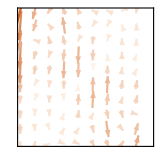

```mathematica
plaquettedvec = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; (* vertex number for the lower left vertex of the plaquette *)
xdvec = (Optdvec1[[llvertex, llvertex+sqrtpts]] + Optdvec1[[llvertex +1, llvertex+sqrtpts+1]])/2;
ydvec = (Optdvec1[[llvertex, llvertex+1]] + Optdvec1[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/2 ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xdvec, ydvec}/h},
{pedge, plaquettes}
];
cmapdvec = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapdvec2 = cmapdvec[(#-minc) / (4.*stepc)]&;

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
xmajor=50;
xminor=10;
ymajor=20;
yminor=1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,""MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdvec = Show[
ListVectorPlot[plaquettedvec,
PlotRange->Transpose[{plaquettedvec[[1]][[1]],plaquettedvec[[-1]][[1]]}],
VectorColorFunction->(cmapdvec2[#5]&),
VectorColorFunctionScaling->False,
VectorPoints->{10,10},
VectorStyle->{Arrowheads[0.06],Thickness[0.01]}
],
FrameStyle->Thick,
Frame->True,
FrameTicks->None(*ft*),
FrameLabel->None(*{""MaTeX["x_1",FontSize->16],MaTeX["x_2",FontSize->16]}*),
ImageSize->160,
AspectRatio->1,
ImagePadding->{{0, 0}, {0, 0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"/Optdvecplot1.pdf",localdvec];
```

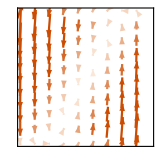

```mathematica
plaquettethermoforce = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; (* vertex number for the lower left vertex of the plaquette *)
xthermoforce=(Thermoforce[[llvertex, llvertex+sqrtpts]] + Thermoforce[[llvertex +1, llvertex+sqrtpts+1]])/2;
ythermoforce=(Thermoforce[[llvertex, llvertex+1]] + Thermoforce[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/2 ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xthermoforce, ythermoforce}/h},
{pedge, plaquettes}
];
cmapdvec = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettethermoforce][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[plaquettethermoforce][[-1]])];

ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
xmajor=50;
xminor=10;
ymajor=20;
yminor=1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,""MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localthermoforce = Show[
ListVectorPlot[plaquettethermoforce,
PlotRange->Transpose[{plaquettethermoforce[[1]][[1]],plaquettethermoforce[[-1]][[1]]}],
VectorColorFunction->(cmapdvec2[#5]&),
VectorColorFunctionScaling->False,
VectorPoints->{10,10},
VectorStyle->{Arrowheads[0.06],Thickness[0.01]}
],
Frame->True,
FrameStyle->Thick,
FrameTicks->None(*ft*),
FrameLabel->None(*{""MaTeX["x_1",FontSize->16],MaTeX["x_2",FontSize->16]}*),
ImageSize->160,
AspectRatio->1,
ImagePadding->{{0, 0}, {0, 0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"/thermoforceplot.pdf",localthermoforce];
```

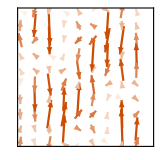

```mathematica
plaquettedvec = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; (* vertex number for the lower left vertex of the plaquette *)
xdvec = (RandOptdvecIni1[[llvertex, llvertex+sqrtpts]] + RandOptdvecIni1[[llvertex +1, llvertex+sqrtpts+1]])/2;
ydvec = (RandOptdvecIni1[[llvertex, llvertex+1]] + RandOptdvecIni1[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/2 ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xdvec, ydvec}/h},
{pedge, plaquettes}
];
cmapdvec = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapdvec2 = cmapdvec[(#-minc) / (4.*stepc)]&;

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
xmajor=50;
xminor=10;
ymajor=20;
yminor=1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,""MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdvec = Show[
ListVectorPlot[plaquettedvec,
PlotRange->Transpose[{plaquettedvec[[1]][[1]],plaquettedvec[[-1]][[1]]}],
VectorColorFunction->(cmapdvec2[#5]&),
VectorColorFunctionScaling->False,
VectorPoints->{10,10},
VectorStyle->{Arrowheads[0.06],Thickness[0.01]}
],
FrameStyle->Thick,
Frame->True,
FrameTicks->None(*ft*),
FrameLabel->None(*{""MaTeX["x_1",FontSize->16],MaTeX["x_2",FontSize->16]}*),
ImageSize->160,
AspectRatio->1,
ImagePadding->{{0, 0}, {0, 0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"/RandOptdvecIni1.pdf",localdvec];
```

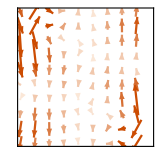

```mathematica
plaquettedvec = Table[
t={Floor[(#-1)/ sqrtplaquettes]+1, Mod[#-1, sqrtplaquettes]+1}&/@pedge;

llvertex = (t[[1,1]]-1)*sqrtpts + t[[1,2]]; (* vertex number for the lower left vertex of the plaquette *)
xdvec = (RandOptdvecEnd1[[llvertex, llvertex+sqrtpts]] + RandOptdvecEnd1[[llvertex +1, llvertex+sqrtpts+1]])/2;
ydvec = (RandOptdvecEnd1[[llvertex, llvertex+1]] + RandOptdvecEnd1[[llvertex + sqrtpts, llvertex+sqrtpts+1]])/2 ;

xcoord = xmin + h[[1]] * t[[1,1]]-(h[[1]]/2);
ycoord = ymin + h [[2]]* t[[1,2]]-(h[[2]]/2);
{{xcoord, ycoord},{xdvec, ydvec}/h},
{pedge, plaquettes}
];
cmapdvec = (Blend[{RGBColor[{255, 245, 235}/255], RGBColor[{204,76,2}/255]},#]&);
minc= Min[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
maxc =Max[Norm[#]&/@(Transpose[plaquettedvec][[-1]])];
ticklocationsc = N[FindDivisions[{minc, maxc}, 5]];

minc = ticklocationsc[[1]];
maxc = ticklocationsc[[-1]];
stepc = (maxc - minc) /10.;
cmapdvec2 = cmapdvec[(#-minc) / (4.*stepc)]&;

xmax = 50.;
xmin = -50.;
ymax = 20.;
ymin = -20.;
xmajor=50;
xminor=10;
ymajor=20;
yminor=1;
majorlen=0.0;
minorlen=0.0;
ft={Flatten[{Table[{i,""MaTeX[i, FontSize->16],{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,MaTeX[j, FontSize->16],{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1],Flatten[{Table[{i,"",{majorlen,0}},{i,xmin,xmax,xmajor}],Table[{i,"",{minorlen,0}},{i,xmin,xmax,xminor}]},1],Flatten[{Table[{j,"",{majorlen,0}},{j,ymin,ymax,ymajor}],Table[{j,"",{minorlen,0}},{j,ymin,ymax,yminor}]},1]};
localdvec = Show[
ListVectorPlot[plaquettedvec,
PlotRange->Transpose[{plaquettedvec[[1]][[1]],plaquettedvec[[-1]][[1]]}],
VectorColorFunction->(cmapdvec2[#5]&),
VectorColorFunctionScaling->False,
VectorPoints->{10,10},
VectorStyle->{Arrowheads[0.06],Thickness[0.01]}
],
FrameStyle->Thick,
Frame->True,
FrameTicks->None(*ft*),
FrameLabel->None(*{""MaTeX["x_1",FontSize->16],MaTeX["x_2",FontSize->16]}*),
ImageSize->160,
AspectRatio->1,
ImagePadding->{{0, 0}, {0, 0}}
]
```

```mathematica
Export[NotebookDirectory[]<>"/RandOptdvecEnd1.pdf",localdvec];
```